```mathematica
(* The vectors *)
w = 1;
b[1] = w{Sqrt[2], 0};
b[2] = w {Sqrt[2]/2, Sqrt[6]/2};
b[3] = w {-Sqrt[2]/2, Sqrt[6]/2};

(* The inner products with {x, y} *)
b1 = b[1].{x, y};
b2 = b[2].{x, y}; 
b3 = b[3].{x, y};  

(* The associated operators *)
Db1 = b[1][[1]] d1 + b[1][[2]] d2;
Db2 = b[2][[1]] d1 + b[2][[2]] d2;
Db3 = b[3][[1]] d1 + b[3][[2]] d2;

(* Derivative of a function f in the direction of a vecor v *)
DirectionalD[f_, v_] := v[[1]] D[f, x] + v[[2]] D[f, y];
```

```mathematica
(* The functions *)
v[x_, y_] := Sum[b[i].b[i] 2/Sinh[b[i].{x, y}]^2, {i, {1, 2, 3}}];
v1[x_, y_] :=b[1].b[1] 2/Sinh[b[1].{x, y}]^2;
v2[x_, y_] :=b[2].b[2] 2/Sinh[b[2].{x, y}]^2;
v3[x_, y_] := b[3].b[3]  2/Sinh[b[3].{x, y}]^2;

f1[x_, y_] :=-b[1].b[1]Coth[b[1].{x, y}] ;
f2[x_, y_] := -b[2].b[2]Coth[b[2].{x, y}];
f3[x_, y_] :=-b[3].b[3]Coth[b[3].{x, y}] ;

g1[x_, y_] := f2[x, y] f3[x, y] ;
g2[x_, y_] := f1[x, y] f3[x, y];
g3[x_, y_] := f1[x, y] f2[x, y];


h[x_, y_] := f1[x, y] f2[x, y] f3[x, y] -4/Sinh[b1]/Sinh[b2]/Sinh[b3];
```

```mathematica
(* Proposition 4.1 *)
Simplify[
-2(D[f1[x, y], x] d1 + D[f1[x, y], y] d2) Db2 Db3
-2 (D[f2[x, y], x] d1 + D[f2[x, y], y] d2) Db1 Db3
- 2(D[f3[x, y], x] d1 + D[f3[x, y], y] d2) Db1 Db2
+ v[x, y] Db1 Db2 Db3
]
```

0

```mathematica
(* Proposition 4.2 *)
Simplify[
-Laplacian[f1[x, y], {x, y}] Db2 Db3
-Laplacian[f2[x, y], {x, y}] Db1 Db3
-Laplacian[f3[x, y], {x, y}] Db1 Db2

-2(D[g1[x, y], x] d1 + D[g1[x, y], y] d2) Db1
-2 (D[g2[x, y], x] d1 + D[g2[x, y], y] d2) Db2
- 2(D[g3[x, y], x] d1 + D[g3[x, y], y] d2) Db3

+ v[x, y](f1[x, y]Db2 Db3 + f2[x, y] Db1 Db3 + f3[x, y]Db1 Db2)
]
```

0

```mathematica
(* Proposition 4.4 *)
N[
Coefficient[
-Laplacian[g1[x, y], {x, y}] Db1
-Laplacian[g2[x, y], {x, y}] Db2
-Laplacian[g3[x, y], {x, y}] Db3

+ v[x, y](g1[x, y]Db1+ g2[x, y] Db2 + g3[x, y]Db3)

-2(D[h[x, y], x] d1 + D[h[x, y], y] d2)

/. {x ->0.11, y->0.022}
, d1]
]
```

0.

```mathematica
coeffd1 = Simplify[
Coefficient[
-Laplacian[g1[x, y], {x, y}] Db1
-Laplacian[g2[x, y], {x, y}] Db2
-Laplacian[g3[x, y], {x, y}] Db3

+ v[x, y](g1[x, y]Db1+ g2[x, y] Db2 + g3[x, y]Db3)

-2(D[h[x, y], x] d1 + D[h[x, y], y] d2)
, d1]
]
```

0

```mathematica
N[
Coefficient[
-Laplacian[g1[x, y], {x, y}] Db1
-Laplacian[g2[x, y], {x, y}] Db2
-Laplacian[g3[x, y], {x, y}] Db3

+ v[x, y](g1[x, y]Db1+ g2[x, y] Db2 + g3[x, y]Db3)

-2(D[h[x, y], x] d1 + D[h[x, y], y] d2)

/. {x ->0.11, y->0.022}
, d2]
]
```

-2.32831×10^-10

```mathematica
(* Check 1st order (algebraically) *)
Simplify[
-Laplacian[g1[x, y], {x, y}] Db1
-Laplacian[g2[x, y], {x, y}] Db2
-Laplacian[g3[x, y], {x, y}] Db3

+ v[x, y](g1[x, y]Db1+ g2[x, y] Db2 + g3[x, y]Db3)

-2(D[h[x, y], x] d1 + D[h[x, y], y] d2)
]
```

0

```mathematica
coeffd2 = Simplify[
Coefficient[
-Laplacian[g1[x, y], {x, y}] Db1
-Laplacian[g2[x, y], {x, y}] Db2
-Laplacian[g3[x, y], {x, y}] Db3

+ v[x, y](g1[x, y]Db1+ g2[x, y] Db2 + g3[x, y]Db3)

-2(D[h[x, y], x] d1 + D[h[x, y], y] d2)
, d2]
]
```

0

```mathematica
(* Check 0th order (numerically first) *)
N[-Laplacian[h[x, y], {x, y}] + v[x, y] h[x, y]/. {x ->0.11, y->0.022}] // Simplify
```

-7.45058×10^-9

```mathematica
(* Check 0th order (algebraically) - runs for a longer time but works on my machine *)
Simplify[
-Laplacian[h[x, y], {x, y}] + v[x, y] h[x, y]
]
```

0

```mathematica
(*** Check the intetwining relation directly ***)

(* The operators *)
HA2m1[g_] := -D[g,x,x]-D[g,y,y]+ v[x, y]g;
DA2m1Laplace[g_] := DirectionalD[DirectionalD[DirectionalD[g,b[3]],b[2]],b[1]]+ f1[x, y]DirectionalD[DirectionalD[g,b[2]],b[3]] + f2[x, y]DirectionalD[DirectionalD[g,b[1]],b[3]]+ f3[x, y]DirectionalD[DirectionalD[g,b[1]],b[2]]+ g1[x, y]DirectionalD[g,b[1]] + g2[x, y]DirectionalD[g,b[2]]+ g3[x, y]DirectionalD[g,b[3]]+ h[x, y] g;
```

```mathematica
(* Check the intertwining relation *)
Simplify[
HA2m1[DA2m1Laplace[g[x, y]]] - DA2m1Laplace[-Laplacian[g[x, y], {x, y}]] 
]
```

0

```mathematica
(**** Obtain the Baker-Akhiezer function PsiA2m1 ****)
X = {x, y};
z = {U, V};
PsiA2m1 = DA2m1Laplace[Exp[X.z]];

ByteCount[PsiA2m1]

Simplify[
PsiA2m1
- (
(b[1].z)(b[2].z)(b[3].z) 
- 2 (b[2].z)(b[3].z) Coth[b1]- 2 (b[1].z)(b[3].z) Coth[b2]- 2 (b[1].z)(b[2].z) Coth[b3]
+4(b[1].z)Coth[b2]Coth[b3]+4(b[2].z)Coth[b1]Coth[b3]+4(b[3].z)Coth[b1]Coth[b2]
- 8Coth[b1] Coth[b2]Coth[b3] - 4/Sinh[b1]/Sinh[b2]/Sinh[b3]
)Exp[X.z]
]

ByteCount[(
(b[1].z)(b[2].z)(b[3].z) 
- 2 (b[2].z)(b[3].z) Coth[b1]- 2 (b[1].z)(b[3].z) Coth[b2]- 2 (b[1].z)(b[2].z) Coth[b3]
+4(b[1].z)Coth[b2]Coth[b3]+4(b[2].z)Coth[b1]Coth[b3]+4(b[3].z)Coth[b1]Coth[b2]
- 8Coth[b1] Coth[b2]Coth[b3] - 4/Sinh[b1]/Sinh[b2]/Sinh[b3]
)Exp[X.z]]

PsiA2m1 = ((b[1].z)(b[2].z)(b[3].z) 
- 2 (b[2].z)(b[3].z) Coth[b1]- 2 (b[1].z)(b[3].z) Coth[b2]- 2 (b[1].z)(b[2].z) Coth[b3]
+4(b[1].z)Coth[b2]Coth[b3]+4(b[2].z)Coth[b1]Coth[b3]+4(b[3].z)Coth[b1]Coth[b2]
- 8Coth[b1] Coth[b2]Coth[b3] - 4/Sinh[b1]/Sinh[b2]/Sinh[b3])Exp[X.z];

PsiA2m1NOuv =((b[1].z)(b[2].z)(b[3].z) 
- 2 (b[2].z)(b[3].z) Coth[b1]- 2 (b[1].z)(b[3].z) Coth[b2]- 2 (b[1].z)(b[2].z) Coth[b3]
+4(b[1].z)Coth[b2]Coth[b3]+4(b[2].z)Coth[b1]Coth[b3]+4(b[3].z)Coth[b1]Coth[b2]
- 8Coth[b1] Coth[b2]Coth[b3] - 4/Sinh[b1]/Sinh[b2]/Sinh[b3])Exp[X.z] /. {U -> 0.5, V -> 0.1} // FullSimplify;
ByteCount[PsiA2m1NOuv]
```

16824

0

11912

4504

```mathematica
(**** Check PsiA2m1 *****)

(* Check that it's an eigeinfunction of the Hamiltonian *)
Simplify[HA2m1[PsiA2m1 ]+(U^2+V^2)PsiA2m1 ]
```

0

```mathematica
(* Check axiomatics *)
N[PsiA2m1 /. { U -> Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m1  /. { U-> -Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]

val1 = PsiA2m1 /. { U -> Sqrt[2]};
val2 = PsiA2m1 /. { U -> -Sqrt[2]};
Simplify[val1 - val2]
```

-39.184

-39.184

0

```mathematica
Solve[b[2].z == 0, {U, V}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{V→-U/(√3)}}

```mathematica
val1 = PsiA2m1 /. { U  ->A+ b[2][[1]], V-> -A/Sqrt[3]+ b[2][[2]]};
val2 = PsiA2m1 /. { U  -> A - b[2][[1]], V-> -A/Sqrt[3]- b[2][[2]]};
FullSimplify[val1 - val2]
```

0

```mathematica
Solve[b[3].z == 0, {U, V}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{V→U/(√3)}}

```mathematica
val1 = PsiA2m1 /. { U  ->A+ b[3][[1]], V-> A/Sqrt[3]+ b[3][[2]]};
val2 = PsiA2m1 /. { U  -> A - b[3][[1]], V-> A/Sqrt[3]- b[3][[2]]};
FullSimplify[val1 - val2]
```

0

```mathematica
(***** Obtain the Baker-Akhiezer function PsiA2m2 ****)
```

```mathematica
Clear[g]
<<DA2m2A2m1.mx;
```

```mathematica
g[x_, y_] :=Evaluate[PsiA2m1];
PsiA2m2 = DA2m2A2m1;
Clear[g]
ByteCount[PsiA2m2]
```

1663856

```mathematica
(**** Check PsiA2m2 *****)

(* Check that it's an eigeinfunction of the Hamiltonian *)
v[x_, y_] := Sum[b[i].b[i] 6/Sinh[b[i].{x, y}]^2, {i, {1, 2, 3}}];
HA2m2[g_] := -D[g,x,x]-D[g,y,y]+ v[x, y]g;
```

```mathematica
N[HA2m2[PsiA2m2 ]+(U^2+V^2)PsiA2m2 /. { U -> 0.22, V->0.1, x -> 0.2, y -> -1} ] 
N[(U^2+V^2)PsiA2m2 /. { U -> 0.22, V->0.1, x -> 0.2, y -> -1} ]
```

-3.72529×10^-9

2609.29

```mathematica
(* Check axiomatics *)
N[PsiA2m2 /. { U -> Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m2  /. { U-> -Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]

N[PsiA2m2 /. { U -> 2Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m2  /. { U-> -2Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]
```

40164.3

40164.3

28449.2

28449.2

```mathematica
N[PsiA2m2 /. { U  ->0.1+ b[2][[1]], V-> -0.1/Sqrt[3]+ b[2][[2]], x -> 0.2, y -> -1}]
N[PsiA2m2  /. {  U  ->0.1-b[2][[1]], V-> -0.1/Sqrt[3]- b[2][[2]], x -> 0.2, y -> -1}]

N[PsiA2m2 /. { U  ->0.1+ 2b[2][[1]], V-> -0.1/Sqrt[3]+ 2b[2][[2]], x -> 0.2, y -> -1}]
N[PsiA2m2  /. {  U  ->0.1-2b[2][[1]], V-> -0.1/Sqrt[3]- 2b[2][[2]], x -> 0.2, y -> -1}]
```

39604.3

39604.3

28278.6

28278.6

```mathematica
N[PsiA2m2 /. { U  ->0.1+ b[3][[1]], V-> 0.1/Sqrt[3]+ b[3][[2]], x -> 0.2, y -> -1}]
N[PsiA2m2  /. {  U  ->0.1-b[3][[1]], V-> 0.1/Sqrt[3]- b[3][[2]], x -> 0.2, y -> -1}]

N[PsiA2m2 /. { U  ->0.1+ 2b[3][[1]], V-> 0.1/Sqrt[3]+ 2b[3][[2]], x -> 0.2, y -> -1}]
N[PsiA2m2  /. {  U  ->0.1-2b[3][[1]], V-> 0.1/Sqrt[3]- 2b[3][[2]], x -> 0.2, y -> -1}]
```

39243.

39243.

27709.5

27709.5

```mathematica
(* Obtain the Baker-Akhiezer function PsiA2m3 *)
Clear[g]
<<DA2m3A2m2.mx;
```

```mathematica
g[x_, y_] :=Evaluate[PsiA2m2];
PsiA2m3 = DA2m3A2m2;
Clear[g]
ByteCount[PsiA2m3 ]
```

232000216

```mathematica
(**** Check PsiA2m3 ****)

(* Check axiomatics *)
N[PsiA2m3 /. { U -> Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m3  /. { U-> -Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]

N[PsiA2m3 /. { U -> 2Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m3  /. { U-> -2Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]

N[PsiA2m3 /. { U -> 3Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m3  /. { U-> -3Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]
```

-1.92462×10^8

-1.92462×10^8

-1.55644×10^8

-1.55644×10^8

-1.10039×10^8

-1.10039×10^8

```mathematica
(* Obtain the Baker-Akhiezer function PsiG2m1m3 *)
Clear[g]
<<DG2m3m1A2m3.mx;
```

```mathematica
PsiA2m3NoUV =N[PsiA2m3 /. { U -> Sqrt[2.], V->0.1}];
ByteCount[PsiA2m3NoUV]
```

108149608

```mathematica
g[x_, y_] := Evaluate[PsiA2m3NoUV] ;
PsiG2m1m3 = DG2m3m1A2m3;
Clear[g]
ByteCount[PsiG2m1m3 ]
```

$Aborted

0

```mathematica
(* Obtain the Baker-Akhiezer function PsiAG2m1 *)
PsiAG2m1 = D0[PsiG2m1m3 ];
ByteCount[PsiAG2m1 ]
```

23506376

```mathematica
DumpSave["PsiAG2m1.mx", PsiAG2m1];
```

```mathematica
DA2m2A2m1
```

```mathematica
(**** Obtain the Baker-Akhiezer function PsiA2m1 ****)
X = {x, y};
z = {U, V};
PsiA2m1 = DA2m1Laplace[Exp[X.z]];

ByteCount[PsiA2m1]

Simplify[
PsiA2m1
- (
(b[1].z)(b[2].z)(b[3].z) 
- 2 (b[2].z)(b[3].z) Coth[b1]- 2 (b[1].z)(b[3].z) Coth[b2]- 2 (b[1].z)(b[2].z) Coth[b3]
+4(b[1].z)Coth[b2]Coth[b3]+4(b[2].z)Coth[b1]Coth[b3]+4(b[3].z)Coth[b1]Coth[b2]
- 8Coth[b1] Coth[b2]Coth[b3] - 4/Sinh[b1]/Sinh[b2]/Sinh[b3]
)Exp[X.z]
]

ByteCount[(
(b[1].z)(b[2].z)(b[3].z) 
- 2 (b[2].z)(b[3].z) Coth[b1]- 2 (b[1].z)(b[3].z) Coth[b2]- 2 (b[1].z)(b[2].z) Coth[b3]
+4(b[1].z)Coth[b2]Coth[b3]+4(b[2].z)Coth[b1]Coth[b3]+4(b[3].z)Coth[b1]Coth[b2]
- 8Coth[b1] Coth[b2]Coth[b3] - 4/Sinh[b1]/Sinh[b2]/Sinh[b3]
)Exp[X.z]]

PsiA2m1 = ((b[1].z)(b[2].z)(b[3].z) 
- 2 (b[2].z)(b[3].z) Coth[b1]- 2 (b[1].z)(b[3].z) Coth[b2]- 2 (b[1].z)(b[2].z) Coth[b3]
+4(b[1].z)Coth[b2]Coth[b3]+4(b[2].z)Coth[b1]Coth[b3]+4(b[3].z)Coth[b1]Coth[b2]
- 8Coth[b1] Coth[b2]Coth[b3] - 4/Sinh[b1]/Sinh[b2]/Sinh[b3])Exp[X.z];

PsiA2m1NOuv =((b[1].z)(b[2].z)(b[3].z) 
- 2 (b[2].z)(b[3].z) Coth[b1]- 2 (b[1].z)(b[3].z) Coth[b2]- 2 (b[1].z)(b[2].z) Coth[b3]
+4(b[1].z)Coth[b2]Coth[b3]+4(b[2].z)Coth[b1]Coth[b3]+4(b[3].z)Coth[b1]Coth[b2]
- 8Coth[b1] Coth[b2]Coth[b3] - 4/Sinh[b1]/Sinh[b2]/Sinh[b3])Exp[X.z] /.  { U -> Sqrt[2.], V->0.1} // FullSimplify;
ByteCount[PsiA2m1NOuv]
```

16824

0

11912

3448

```mathematica
(**** Check PsiA2m1 *****)

(* Check that it's an eigeinfunction of the Hamiltonian *)
Simplify[HA2m1[PsiA2m1 ]+(U^2+V^2)PsiA2m1 ]
```

0

```mathematica
(* Check axiomatics *)
N[PsiA2m1 /. { U -> Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m1  /. { U-> -Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]

val1 = PsiA2m1 /. { U -> Sqrt[2]};
val2 = PsiA2m1 /. { U -> -Sqrt[2]};
Simplify[val1 - val2]
```

-39.184

-39.184

0

```mathematica
Solve[b[2].z == 0, {U, V}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{V→-U/(√3)}}

```mathematica
val1 = PsiA2m1 /. { U  ->A+ b[2][[1]], V-> -A/Sqrt[3]+ b[2][[2]]};
val2 = PsiA2m1 /. { U  -> A - b[2][[1]], V-> -A/Sqrt[3]- b[2][[2]]};
FullSimplify[val1 - val2]
```

0

```mathematica
Solve[b[3].z == 0, {U, V}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{V→U/(√3)}}

```mathematica
val1 = PsiA2m1 /. { U  ->A+ b[3][[1]], V-> A/Sqrt[3]+ b[3][[2]]};
val2 = PsiA2m1 /. { U  -> A - b[3][[1]], V-> A/Sqrt[3]- b[3][[2]]};
FullSimplify[val1 - val2]
```

0

```mathematica
(***** Obtain the Baker-Akhiezer function PsiA2m2 ****)
```

```mathematica
Clear[g]
<<DA2m2A2m1.mx;
```

```mathematica
g[x_, y_] :=Evaluate[PsiA2m1NOuv];
PsiA2m2Nouv =FullSimplify[ DA2m2A2m1];
Clear[g]
ByteCount[PsiA2m2Nouv]
```

$Aborted

706112

```mathematica
(**** Check PsiA2m2 *****)

(* Check that it's an eigeinfunction of the Hamiltonian *)
v[x_, y_] := Sum[b[i].b[i] 6/Sinh[b[i].{x, y}]^2, {i, {1, 2, 3}}];
HA2m2[g_] := -D[g,x,x]-D[g,y,y]+ v[x, y]g;
```

```mathematica
N[HA2m2[PsiA2m2 ]+(U^2+V^2)PsiA2m2 /. { U -> 0.22, V->0.1, x -> 0.2, y -> -1} ] 
N[(U^2+V^2)PsiA2m2 /. { U -> 0.22, V->0.1, x -> 0.2, y -> -1} ]
```

-3.72529×10^-9

2609.29

```mathematica
(* Check axiomatics *)
N[PsiA2m2 /. { U -> Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m2  /. { U-> -Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]

N[PsiA2m2 /. { U -> 2Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m2  /. { U-> -2Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]
```

40164.3

40164.3

28449.2

28449.2

```mathematica
N[PsiA2m2 /. { U  ->0.1+ b[2][[1]], V-> -0.1/Sqrt[3]+ b[2][[2]], x -> 0.2, y -> -1}]
N[PsiA2m2  /. {  U  ->0.1-b[2][[1]], V-> -0.1/Sqrt[3]- b[2][[2]], x -> 0.2, y -> -1}]

N[PsiA2m2 /. { U  ->0.1+ 2b[2][[1]], V-> -0.1/Sqrt[3]+ 2b[2][[2]], x -> 0.2, y -> -1}]
N[PsiA2m2  /. {  U  ->0.1-2b[2][[1]], V-> -0.1/Sqrt[3]- 2b[2][[2]], x -> 0.2, y -> -1}]
```

39604.3

39604.3

28278.6

28278.6

```mathematica
N[PsiA2m2 /. { U  ->0.1+ b[3][[1]], V-> 0.1/Sqrt[3]+ b[3][[2]], x -> 0.2, y -> -1}]
N[PsiA2m2  /. {  U  ->0.1-b[3][[1]], V-> 0.1/Sqrt[3]- b[3][[2]], x -> 0.2, y -> -1}]

N[PsiA2m2 /. { U  ->0.1+ 2b[3][[1]], V-> 0.1/Sqrt[3]+ 2b[3][[2]], x -> 0.2, y -> -1}]
N[PsiA2m2  /. {  U  ->0.1-2b[3][[1]], V-> 0.1/Sqrt[3]- 2b[3][[2]], x -> 0.2, y -> -1}]
```

39243.

39243.

27709.5

27709.5

```mathematica
(* Obtain the Baker-Akhiezer function PsiA2m3 *)
Clear[g]
<<DA2m3A2m2.mx;
```

```mathematica
g[x_, y_] :=Evaluate[PsiA2m2Nouv];
PsiA2m3Nouv = DA2m3A2m2;
Clear[g]
ByteCount[PsiA2m3Nouv]
```

117086224

```mathematica
(**** Check PsiA2m3 ****)

(* Check axiomatics *)
N[PsiA2m3 /. { U -> Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m3  /. { U-> -Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]

N[PsiA2m3 /. { U -> 2Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m3  /. { U-> -2Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]

N[PsiA2m3 /. { U -> 3Sqrt[2.], V->0.1, x -> 0.2, y -> -1}]
N[PsiA2m3  /. { U-> -3Sqrt[2.],V->0.1, x -> 0.2, y -> -1}]
```

-1.92462×10^8

-1.92462×10^8

-1.55644×10^8

-1.55644×10^8

-1.10039×10^8

-1.10039×10^8

```mathematica
(* Obtain the Baker-Akhiezer function PsiG2m1m3 *)
Clear[g]
<<DG2m3m1A2m3.mx;
```

```mathematica
PsiA2m3NoUV =N[PsiA2m3 /. { U -> Sqrt[2.], V->0.1}];
ByteCount[PsiA2m3NoUV]
```

108149608

```mathematica
g[x_, y_] := Evaluate[PsiA2m3NoUV] ;
PsiG2m1m3 = DG2m3m1A2m3;
Clear[g]
ByteCount[PsiG2m1m3 ]
```

$Aborted

0

```mathematica
(* Obtain the Baker-Akhiezer function PsiAG2m1 *)
PsiAG2m1 = D0[PsiG2m1m3 ];
ByteCount[PsiAG2m1 ]
```

23506376

```mathematica
DumpSave["PsiAG2m1.mx", PsiAG2m1];
```

```mathematica
DA2m2A2m1
```

```mathematica
(* Try numerical derivatives *)
Needs["NumericalCalculus`"]
```

```mathematica
ND[Evaluate[PsiA2m3Nouv /. {y -> 1}], x, 2]
```

-3.32021×10^8

```mathematica
f[x_] := x^3 + y x;
l=Table[f[x] /. y -> 200,{x,0,10,.1}];
pad=10;
```

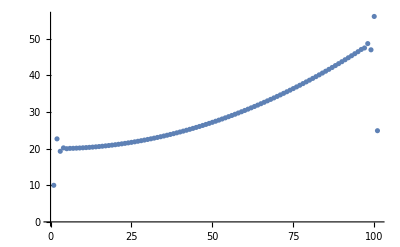

```mathematica
dl=DerivativeFilter[l,{1}];

ListPlot[dl]
```

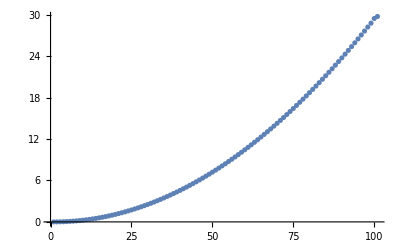

```mathematica
dl=With[{pad=10},ArrayPad[DerivativeFilter[ArrayPad[l,pad,"Extrapolated"],{1}],-pad]];

ListPlot[dl]
```